```mathematica
g[s_,n_]:=N[1/(1-2^(1-s))∑_(k=0)^n 1/2^(k+1)∑_(i=0)^k (-1)^i Binomial[k,i] (i+1)^-s]
```

```mathematica
zerig[x_,n_]:= g[0.5+ x I,n]
```

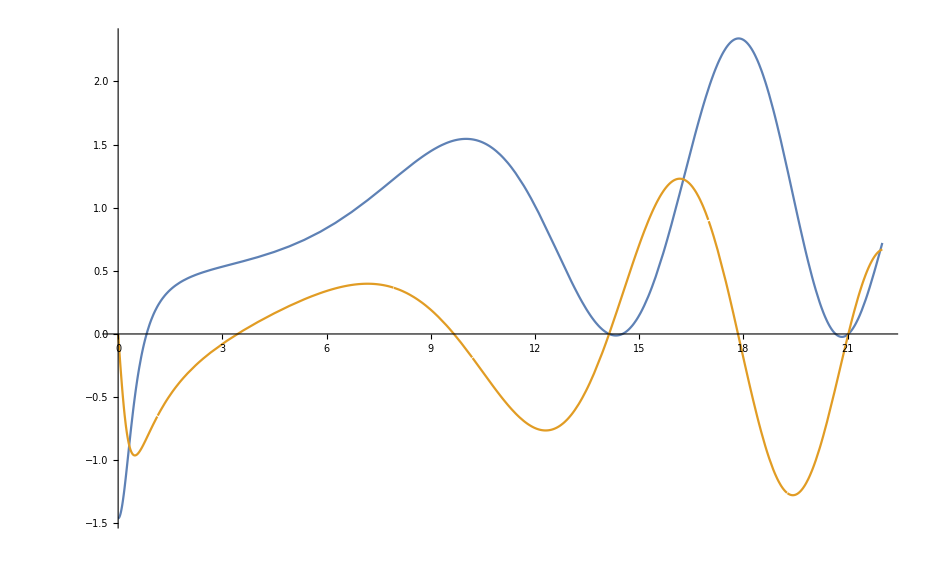

```mathematica
Plot[{Re[zerig[x,40]],Im[zerig[x,40]]},{x,0,22}]
```

```mathematica
N[ZetaZero[2]]
```

0.5+21.022 ⅈ